```mathematica
Style["Simon Lab",FontSize->22,FontFamily->"Helvetica Neue"]
Style["Simon Lab",FontSize->22,FontFamily->"Times New Roman"]
Style["Simon Lab",FontSize->22,FontFamily->"Latin Modern Roman"]
```

Simon Lab

Simon Lab

```mathematica
⟨χ|ψ⟩
```

Simon Lab

```mathematica
TheColor=White;
jLogo=Graphics[{
(*Opacity[0.0],RGBColor[0.37,0.14,0.],Rectangle[{0,9},{20,11}],*)
Opacity[0.0],
White,Rectangle[{0,0},{20,20}],
Opacity[1.0],Text[Style["Simon Lab⟩⟨Simon Lab",FontColor->TheColor,FontSize->28,FontFamily->"Gotham",FontWeight->700],{10,10}],
Opacity[1.0],Text[Style["⟩⟨",FontColor->TheColor,FontSize->28,FontFamily->"Gotham",FontWeight->5000],{10,10}],
TheColor,Thick,
Line[{{-75,3},{-75,16}}],
Line[{{94,3},{94,16}}],
(*Line[{{19,10.7},{19,9.4}}],*)
},ImageSize->{400,38},PlotRange->{{-100,100},{-2,20}}]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["SimonLab.png",jLogo,Background->None,ImageSize->{400,38}];
```

```mathematica
jLogo=Graphics[{
(*Opacity[0.0],RGBColor[0.37,0.14,0.],Rectangle[{0,9},{20,11}],*)
Opacity[0.0],
White,Rectangle[{0,0},{20,20}],
Opacity[1.0],Text[Style["Simon Lab⟩⟨Simon Lab",FontColor->TheColor,FontSize->6*28,FontWeight->700,FontFamily->"Gotham"],{10,10}],
Opacity[1.0],Text[Style["⟩⟨",FontColor->TheColor,FontSize->28,FontFamily->"Gotham",FontWeight->5000],{10,10}],
TheColor,Thickness[.0075],
Line[{{-75,3},{-75,16}}],
Line[{{94,3},{94,16}}],
(*Line[{{19,10.7},{19,9.4}}],*)
},ImageSize->6{400,38},PlotRange->{{-100,100},{-2,20}}]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["SimonLab600.png",jLogo,Background->None,ImageSize->6{400,38}];
```

```mathematica
NotebookDirectory[]
```

/Users/jon/Dropbox/Faculty Stuff/Simonlab Website Materials/NewWebsite_D1/template/MakeLogo/

```mathematica
r=Rasterize[Pane[Style["Mathematica  Mathematica ",128],2100]];

text=SetAlphaChannel[r,ColorNegate[r]];

g=ParametricPlot3D[{ρ,.5 θ Cos[π/2+ArcTan[ρ]],.5θ Sin[π/2+ArcTan[ρ]]},{ρ,-20π,20π},{θ,-1,1},PlotStyle->Darker[Red],Lighting->"Neutral",Mesh->None,MeshShading->None,PlotRange->All,Boxed->False,Axes->False,Background->None,ViewVector->{0,1,0},ViewVertical->{0,1,0}]
```

-Graphics3D-

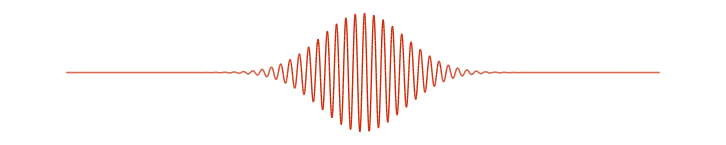

```mathematica
dβ=.003;
f[β_]:=Exp[-(β-5)^2]Cos[40β];
Graphics[{
RGBColor[0.8,0.14,0.],
Table[Line[{{ββ,f[ββ]},{ββ+dβ,f[ββ+dβ]}}],{ββ,0,10,dβ}]
}]
```

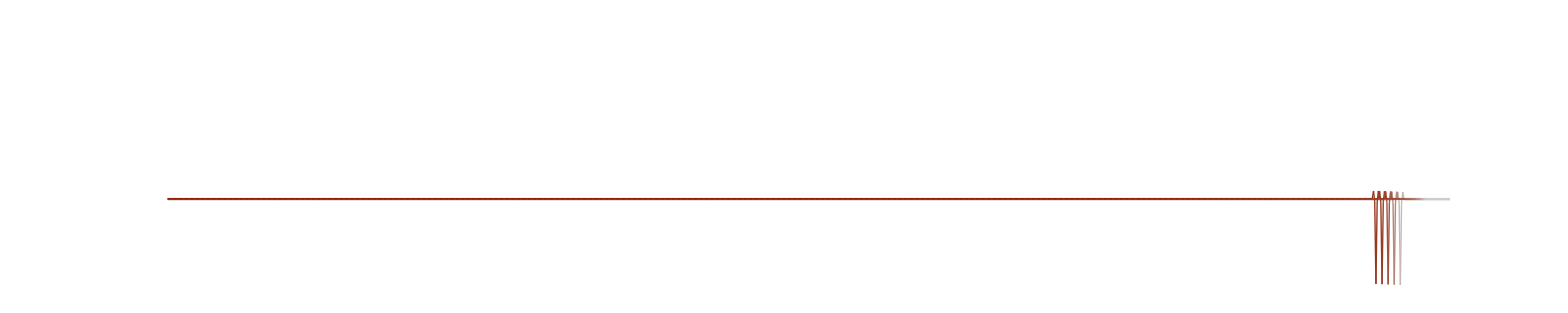

```mathematica
dβ=.1;
f[β_]:=-Exp[-40(β)^2]Cos[11(β)];
f[β_]:=-Exp[-40(β)^2];
f[β_]:=-Exp[-60(β)^2]Cos[15(β)];
PhotonMI=Graphics[{
RGBColor[0.8,0.14,0.],
Table[{Table[{Darker[Lighter[RGBColor[0.7,0.14,0.],Max[1+ArcTan[(ββ-3.)]/(π/2),.3(μ+1)]],.2],Line[{{ββ,-.003μ+f[ββ-.5μ]},{ββ+dβ,-.003μ+f[ββ+dβ-.5μ]}}]},{ββ,-100,8,dβ}]},{μ,2,-2,-1}]
},PlotRange->{{-102,3},{-1,2.0}},ImageSize->1801]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Pulse-HR-right.png",PhotonMI,Background->None,ImageResolution->72];
```

```mathematica
1080/3.
```

360.

```mathematica
569*312/300.
```

591.76

```mathematica
960*312/300.
```

998.4

```mathematica
549*312/300.
```

570.96

```mathematica
1800*312/300.
```

1872.

```mathematica
648*312/300.
```

673.92

```mathematica
1548*375/300.
```

1935.

```mathematica
248*375/300.
```

310.

```mathematica
248*375/300.
```

310.

```mathematica
2785*312/300.
```

2896.4

```mathematica
251. 312/300
```

261.04

```mathematica
Graphics[
```